Worksheet 1, Math 152      *      D. Maslanka      *     Fall 2015

THE NUMBER  e  AS A LIMIT,
LOGARITHMIC AND EXPONENTIAL FUNCTIONS

Goals:  In this worksheet two limits will be described, each of which converges to Euler's   
            number,  ⅇ.  In the exercises we will use a limit formulation to obtain a rational   
            approximation for  ⅇ.  Other  Mathematica  applications related to the exponential 
            and logarithmic functions will also be examined.

                         
Recall that  e  has been defined as the unique real number whose natural logarithm is equal to
one. Using Mathematica syntax, we may indicate this condition with the equation:      
  
  			                  log ⅇ = 1. 
  					
It follows immediately from this definition that :

lim_(h→0) (1+h)^(1/h)  =  ⅇ .

To see this, let   f ( x ) = log x , then   f ' ( x ) = 1/x  for all  x > 0. In particular,   f ' ( 1 ) = 1.  
That is,

lim_(h→0) (f(1+h)-f(1))/h==1

lim_(h→0) (log(1+h)-log(1))/h==1

and since  log ( 1 )  =  0 , we have

lim_(h→0) 1/h log ( 1 + h ) = 1

Equivalently, due to the Power Law property for natural logarithms, this limit may be written as:

lim_(h→0) (log(1+h))^(1/h) = 1

So by the continuity of the natural logarithmic function, we must have that

log  [lim_(h→0) (1+h)^(1/h)] = 1

Then since the natural logarithm is a one-to-one function, we may conclude that

lim_(h→0) (1+h)^(1/h)  =  ⅇ .                ( * )

Now set  x = 1/h  and observe that as  h → 0  from the right, then  x → ∞ , so we have upon 
substitution into  ( * )  that

lim_(x→∞) (1+1/x)^x==ⅇ  .                  ( ** )

(Please click on the link:  notes1  for details on irrational powers.)

In  Mathematica's  syntax, the real number  ⅇ  may be denoted by Exp[1], and in order to 
designate the exponential function:   f ( x ) = ⅇ^x , we enter

			     f[x_]:=Exp[x]. 
			     
The natural logarithmic function:  g ( x ) = log ( x )  may be denoted by  

			    g[x_]:=Log[x].   
			    
It should be emphasized that many authors write  log ( x ) to denote the common logarithm 
of  x  ( i.e.,  the base 10 logarithm of  x ). However, in  Mathematica,  log ( x )  always
refers to the natural logarithm of  x . 
The base  a  logarithm, log_a(x) ,  is written as   Log[a,x] in  Mathematica  syntax. 
To illustrate the above remarks, we define and graph some exponential and logarithmic pairs.
First, we define the inverse pair of functions in Mathematica:

```mathematica
f[x_]:=Exp[x]
g[x_]:=Log[x]
```

To view these definitions, in text form, we may enter:

```mathematica
"f(x)="f[x]
"g(x)="g[x]
```

Now we plot the pair in the plane region where   - 4 <  x  <  10  and   - 4 <  y  <  10 with the 
instruction:

```mathematica
Plot[{f[x],g[x]},{x,-4,10},PlotRange->{-4,10},PlotStyle->{{Blue,Thickness[0.004]},{Darker[Magenta],Thickness[0.004]}},AspectRatio->Automatic,AxesLabel->{x,y}]
```

In the above command, note that the option AspectRatio ⟶ Automatic  was used to 
make certain that unit lengths are measured according to the same scale on both the horizontal 
and the vertical axes. 
   
In order to label the pair of curves in the figure, we may first give a name to the graph, write
Text instructions (a part of the Graphics package) and then utilize the Show instruction to 
merge the graph with the text as follows:

```mathematica
fgGraph=Plot[{f[x],g[x]},{x,-4,10},PlotRange->{-4,10},PlotStyle->{{Blue,Thickness[0.004]},{Darker[Magenta],Thickness[0.004]}},AspectRatio->Automatic,AxesLabel->{x,y}];
T1=Graphics[Text[Style["y=ⅇ^x",Bold,Italic,Small,Blue],{2.75,6}]];
T2=Graphics[Text[Style["y=log(x)",Bold,Italic,Small,Darker[Magenta]],{6,2.5}]];
Show[fgGraph,T1,T2]
```

Note that in the figure the label " y = ⅇ^x "  is centered at the point  ( 2.75 , 6 ) while 
" y = log ( x ) "  is centered at the point ( 6 , 2.5 ).

Finally, we choose to add a plot of the identity function to our figure .

```mathematica
IdentityGraph=Plot[{x},{x,-3,9},PlotStyle->{Darker[Red],Dashed}];
Show[fgGraph,T1,T2,IdentityGraph]
```

Note that the PlotStyle option:  Dashed  was used to make the identity graph appear
as a broken, rather than a solid, line in the figure.

Now we plot a second inverse pair of logarithmic and exponential functions:

```mathematica
m[x_]:=(1/2)^x
n[x_]:=Log[1/2,x]
mGraph=Plot[m[x],{x,-2,4},PlotRange->{-2,2},PlotStyle->{Orange,Thickness[0.004]},AspectRatio->Automatic,AxesLabel->{x,y}];
nGraph=Plot[n[x],{x,-2,4},PlotRange->{-2,2},PlotStyle->{Darker[Green],Thickness[0.004]},AspectRatio->Automatic];
IdentityGraph=Plot[{x},{x,-1.5,4},PlotStyle->{Darker[Red],Dashed}];
T3=Graphics[Text[Style["y = 1/2^x",Bold,Italic,Small,Darker[Orange]],{-1,1.2}]];
T4=Graphics[Text[Style["y = log_(FractionBox[1, 2])(x)",Bold,Italic,Small,Darker[Green]],{3.6,-1.5}]];
Show[mGraph,nGraph,IdentityGraph,T3,T4]
```

______________________________________
Exercises

1.  In this problem, you will approximate the number  ⅇ  numerically.
     ( a )  Define the function:  f ( x ) = (1+1/x)^x  and the constant function:  g ( x ) =  ⅇ  	  
     	  using Mathematica

```mathematica
f[x_]:=(1+1/x)^x
```

```mathematica
g[x_]:=(ⅇ)
```

( b )   Sketch a graph of  the functions  f  and  g  defined in part  (a)  over the interval
              0  <  x  <  50  and explain, in words, the relationship between these two graphs.
              Hint: Try using the option AspectRatio→1/2 in your Plot instruction.

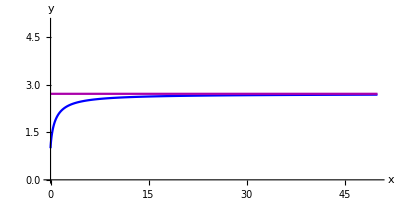

```mathematica
Plot[{f[x],g[x]},{x,0,50},PlotRange->{0,5},PlotStyle->{{Blue,Thickness[0.004]},{Darker[Magenta],Thickness[0.004]}},AspectRatio->1/2,AxesLabel->{x,y}]
```

( c )   Execute the following sequence of instructions within a single cell in order to find 
             the smallest integer  P  which satisfies the inequality:
                                              ⅇ - f ( P ) <  1/100 .

```mathematica
P=1;(* a counter *)
While[Exp[1]-f[P]>=1/100,P=P+1];
P  "=P"
```

135 =P

( d )   Find the least integers  Q  and  R  such that:
		    ⅇ - f ( Q ) <  1/1000 = 10^-3
		    ⅇ - f ( R ) <  1/10000= 10^-4
	   by using  While instruction as in part ( c ).

```mathematica
R=1;Q=1;
While[Exp[1]-f[Q]≥1/1000,Q=Q+1];
While[Exp[1]-f[R]≥1/10000,R=R+1];
Q "=Q" 
R"=R"
```

1359 =Q

13591 =R

( e )   The values:  f ( P ),  f ( Q ) and  f ( R )  are successively better approximations
               to the number  ⅇ . Use  Mathematica to find decimal representations for these 
               values.
                Note that in Mathematica the instruction: N[f[P]] yields a decimal
                representation of the number  f[P] .

```mathematica
N[f[P]]
```

2.70828

```mathematica
N[f[Q]]
```

2.71728

```mathematica
N[f[R]]
```

2.71818

2.  When studying Taylor Series in Chapter 11, it will be shown that the sum:

                            1 + 1/(1!) + 1/(2!)  + 1/(3!)  +  . . .  + 1/(n!)      (*)
                         
       converges to the number ⅇ  as  n → ∞.
      
       Recall that k factorial, k ! ,  is defined by:
       
                        k !  =  1 × 2  ×  3  ×  . . . × k   for any positive integer  k  
              and     0 !  =  1 .
              
     The above sum  (*)  may be described in  Mathematica, as the function, Z( n ), where:

```mathematica
Z[n_]:=Sum[1/k!,{k,0,n}]
```

To view the formula for  Z(n) , in sigma notation, execute the following instruction:

```mathematica
TraditionalForm[HoldForm[Sum[1/k!,{k,0,n}]]]
```

∑_(k=0)^n 1/(k!)

( a )   Use a  While loop to find the least integer  n  such that
              Z( n ) differs from  ⅇ  by less than 1/1000.

```mathematica
n=1;
While[ⅇ-Z[n]≥1/1000,n=n+1];
n "=n"
```

6 =n

( b )   Use the approach specified in part  ( a )  to find the least integer  n  such that
              Z( n )  differs from  ⅇ  by less than  1/10000.

```mathematica
n=1;
While[ⅇ-Z[n]≥1/10000,n=n+1];
n "=n"
```

7 =n

( c )  Based on your findings in problems 1 and 2, which of the two sequences:

                       { (1+1/n)^n }_(n-1)^(+∞)         or        {1+1/(1!) + 1/(2!)  + 1/(3!)+   . . .  +1/(n!)}_(n=1)^(+∞)
            
             appears to converge more quickly to the number  ⅇ ?
       
           {1+1/(1!) + 1/(2!)  + 1/(3!)+   . . .  +1/(n!)}_(n=1)^(+∞) appears to converge more quickly to ⅇ.
           
  3.  ( a )  Use the fact that :

ln n  =∫_1^n 1/t ⅆt

and a pair of associated right and left hand Riemann sums to explain, in words,  why
               the following inequality is valid for any integer n ⩾ 2:   
                
                1/2 + 1/3  + 1/4  +  . . .  + 1/n  <   ln n   <  1 + 1/2 + 1/3    +  . . .  +  1/(n-1)  .                     
              Hint: Use the figure below for reference in this problem. You need not apply any
                       Mathematica instructions in your answer.
                       
                  The reimann sum on the left will be slightly less than the reimann sum on the right as the left one uses a right point to measure the displacement and the right funciton uses the left point, therefore getting a larger amount. Ln(n) is the actual number and not the approximation, therefore it is between the two.

-Graphics-

( b )   Substitute 1,000,000 for  n  in the inequality in part (a) and then apply the  
	       NSum instruction appropriately to obtain upper and lower approximate bounds 
	       on the value of  ln ( 1 000 000) .

```mathematica
NSum[Z[1000000],{n,0,1000000}]
```

2.71828×10^6

4.  Apply the Disc Method and Mathematica to obtain and evaluate an integral expression 
        for the volume of the solid generated by rotating the region bounded by: 
                             y  =  ⅇ^( -x^2) ,    y  =  0 ,  x = 0  and  x  =  1  
        about the  y -axis. 
        (Refer to section 5.2 of the Stewart Text for reference, or click on the link:
         notes2  for help with this topic.)
                   
        In our case,

Volume  = ∫_0^1 π[r(y)]^2 ⅆy

where  r ( y_o ) denotes the radius of the cross-section of the solid in the plane
            which is both perpendicular to the y-axis and is y_o units above the x-axis.)
       -Graphics3D-

```mathematica
∫_0^1 π((ⅇ^(-y^2)))^2 ⅆy
```

(π^(3/2) Erf[√2])/(2 √2)